# Stereo Pixel All Tests

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True];
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
NotebookSave[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
$Path=Append[$Path,FileNames["*",{ParentDirectory[]}]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalStereoAll`"
```

## read

```mathematica
read[set_,num_,reduce_,corf_]:=Module[{ia,ib,id,rgb2d,reduire,clean,io,left,right,disp,occ, frame, base,fileleft,fileright},(

base="D:\MastersMathematica\Data\Sintel";

frame="frame_"<>num<>".png";
fileleft=corf<>"_left";
fileright=corf<>"_right";
left=FileNameJoin[{base,"training",fileleft,set,frame}];
right=FileNameJoin[{base,"training",fileright,set,frame}];
disp=FileNameJoin[{base,"training","disparities",set,frame}];
occ=FileNameJoin[{base,"training","occlusions",set,frame}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];
reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];
ia=reduire[ColorConvert[clean@Import[left],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[right],"GrayScale"],reduce];
id=reduire[Image[
rgb2d[Flatten[N@ImageData[clean@Import[disp],"Byte"],{{3},{1},{2}}]]
],reduce]/reduce;
io=reduire[ColorConvert[clean@Import[occ],"GrayScale"],reduce];
read[{left,right,disp,occ},reduce]={ia,ib,id,io};

{ia,ib,id,io}
)];
```

## Data 1

```mathematica
d=1;

(* downscaling *)
r=2;
{ia,ib,id,io}=read["bamboo_1","0001",r,"clean"]

MinMax[id]

(* a reduction of 6 is {173,73} *)
(*{ia,ib,id,io}=ImageCrop[#,{173,73}]&/@{ia,ib,id,io}*)

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=150/r;
ny=350/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}
MinMax[id]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{0.136895,38.6009}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,1},{103,1},{103,1},{103,1}}

{4.97135,10.5861}

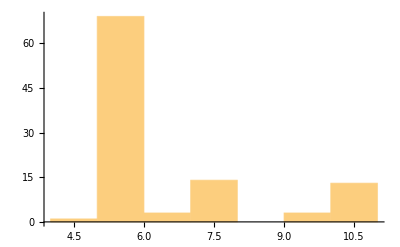

{4.97135,10.5861}

```mathematica
Histogram[Flatten[ImageData[id]]]
minmaxid=MinMax[Flatten[ImageData[id]]]
```

## Pixel test

```mathematica
pixelTest[p0_,prange_,{lvlmin_,lvlmax_},pyrfunctions_,threshold_,mode_]:=Block[{},(
(* Import mode of interest *)
Get["pyramidalCyclope1DLK"<>mode<>"`"];

(* Get all values of 10 iterations *)
(*Any time we call the methods we have to give threshold accordint to the min level *)
pixelIterGraphics[10, p0,prange, lvlmax,pyrfunctions[[lvlmin;;lvlmax]],threshold*2^(-lvlmin+1)]

)]

pixelTest::usage"
Input-> [p0, prange, maxlvl, pyrfunctions, threshold, mode]
Output-> Finds the iterations to calculate a solution for the given pixel p0
and for given levels of pyrfunctions
";
```

```mathematica
pyr12=Flatten[{pyrFuncGen[ImageData[ia][[1]],5],pyrFuncGen[ImageData[ib][[1]],5]},{{2},{1},{3}}];
```

```mathematica
p=24;
lvlmin=4;
lvlmax=5;
```

```mathematica
(*mode="OverConstrained";*)
(*mode="SemiConstrained"; *)
mode="Constrained"; 
(* mode="ConstrainedSign"; *) (*no*)
(* mode="ConstrainedSign2Left"; *) (*no*)
(* mode="ConstrainedSign2Right"; *)(*no*)
ListAnimate[pixelTest[p,20,{lvlmin,lvlmax},pyr12,0.01,mode]]
```